# Cuaderno de Prácticas

## MATEMÁTICAS DISCRETAS

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 7

```mathematica
ORDEN[A_,R_]:=Module[{falloReflexiva,falloAntisimetrica,falloTransitiva},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
COCIENTE[A_,R_]:=Module[{CONTADORi,CONTADORj,anadir},cociente={{A[[1]]}};
Do[anadir=True;
Do[If[Intersection[{{A[[CONTADORi]],cociente[[CONTADORj]][[1]]}},R]≠{},AppendTo[cociente[[CONTADORj]],A[[CONTADORi]]];
anadir=False;
Break[];];,{CONTADORj,1,Length[cociente]}];
If[anadir,AppendTo[cociente,{A[[CONTADORi]]}];];,{CONTADORi,2,Length[A]}];
cociente];
```

```mathematica
COTASSUPERIORES[A_,B_,R_]:=Module[{cotassuperiores,csuper,n,m},cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
cotassuperiores]
```

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},cotassuperiores={};Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];supremo={};Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];supremo]
```

```mathematica
COTASINFERIORES[A_,B_,R_]:=Module[{cotasinferiores,cinfer,n,m},cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
cotasinferiores]
```

```mathematica
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},cotasinferiores={};Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];infimo={};Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo]
```

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales]
```

### Ejercicio 8.4.

Calcular el diagrama de orden de P({a,b,c}) (siendo a, b, c los tres primeros números distintos de tu DNI)

```mathematica
X=Subsets[{1,3,4}];
R={};
For[i=1,i≤Length[X],i++,
	For[j=1,j≤Length[X],j++,
			If[SubsetQ[X[[j]],X[[i]]],(*Si Xi es subconjunto de Xj*)
				AppendTo[R,{X[[i]],X[[j]]}](*Añado a R la pareja (Xi,Xj)*)
			]
		]
	]
R
```

{{{},{}},{{},{1}},{{},{3}},{{},{4}},{{},{1,3}},{{},{1,4}},{{},{3,4}},{{},{1,3,4}},{{1},{1}},{{1},{1,3}},{{1},{1,4}},{{1},{1,3,4}},{{3},{3}},{{3},{1,3}},{{3},{3,4}},{{3},{1,3,4}},{{4},{4}},{{4},{1,4}},{{4},{3,4}},{{4},{1,3,4}},{{1,3},{1,3}},{{1,3},{1,3,4}},{{1,4},{1,4}},{{1,4},{1,3,4}},{{3,4},{3,4}},{{3,4},{1,3,4}},{{1,3,4},{1,3,4}}}

```mathematica
ORDEN[X,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

Diagrama de orden:

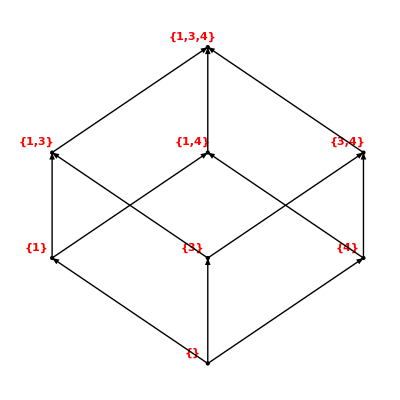

```mathematica
A=X;
R;(*Calculada anteriormente*)
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

### Ejercicio 8.8.

En el conjunto A={1,2,3,4} se establece la relación binaria
R={(1,1),(2,2),(2,3),(2,4),(3,2),(3,3)(3,4),(4,2),(4,3),(4,4)}
Justificar que es una relación de equivalencia y calcular el conjunto cociente.

```mathematica
A={1,2,3,4};
R={{1,1},{2,2},{2,3},{2,4},{3,2},{3,3},{3,4},{4,2},{4,3},{4,4}};
```

```mathematica
AnalisisRB[A,R]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica, falla en los pares: {{2,3},{2,4},{3,2},{3,4},{4,2},{4,3}}

R es una relación de equivalencia

R no es relación de orden

```mathematica
COCIENTE[A,R]
```

{{1},{2,3,4}}

### Ejercicio 8.14

Sea X = {a,b,c,d,e,f} junto con la ordenación dada por el siguiente diagrama:
-Graphics-
Sea Y=[b,f,e} y Z={e,b,c,a} subconjuntos de X. Se pide:

```mathematica
X={a,b,c,d,e,f};
Y={b,f,e};
Z={e,b,c,a};
R={{f,f},{f,e},{f,d},{f,b},{f,c},{f,a},
	{e,e},{e,c},{e,b},{e,a},
	{d,d},{d,b},{d,a},
	{b,b},{b,a},{c,c},{a,a}};
```

a) Cotas superiores e inferiores de Y y de Z . ¿Existen supremo e ínfimo?

```mathematica
COTASSUPERIORES[Y,Z,R]
SUPREMO[Y,Z,R]
```

{a,b}

{b}

```mathematica
COTASINFERIORES[Y,Z,R]
INFIMO[Y,Z,R]
```

{f}

{f}

b) Máximos y mínimos de Y y Z

c) Elementos maximales y minimales de X, Y y Z

```mathematica
MAXIMALES[X,R]
MINIMALES[X,R]
```

{a,c}

{f}

```mathematica
MAXIMALES[Y,R]
MINIMALES[Y,R]
```

{b}

{f}

```mathematica
MAXIMALES[Z,R]
MINIMALES[Z,R]
```

{c,a}

{e}

d) Representar con Mathematica el diagrama de orden X, Y y Z .

Diagrama de orden:

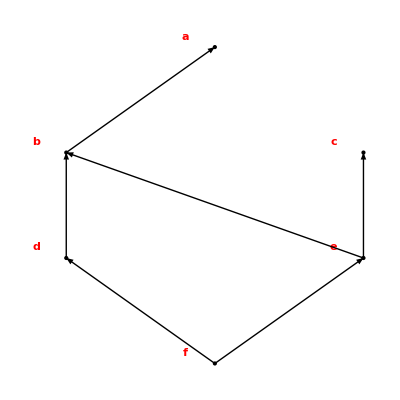

```mathematica
A=X;
R;(*Calculada anteriormente*)
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

### Ejercicio 2 de la Extraordinaria 2 del 23/24

Definir una relación de orden en el conjunto X = P ({∅})*𝔹2 verificando que existe un único elemento de X que sea a la vez maximal y minimal . Hacer todas las comprobaciones . Dibujar el diagrama de orden y razonar si X está bien ordenado

```mathematica
A=Subsets[{{}}];
B={0,1};
cartesiano={};
Do[Do[AppendTo[cartesiano,{A[[i]],B[[j]]}],{i,1,Length[A]}];,{j,1,Length[B]}];
X=cartesiano
```

{{{},0},{{{}},0},{{},1},{{{}},1}}

```mathematica
R={ {{{},0},{{},0}}, {{{{}},0},{{{}},0}} , {{{},1},{{},1}} , {{{{}},1},{{{}},1}} ,
	{ {{},0} , {{{}},0} } , { {{{}},0} , {{},1} } , { {{{}},0} , {{},1}}};
ORDEN[A,R]
```

R no es reflexiva, falla en los elementos: {{},{{}}}

R es antisimétrica

R no es transitiva, falla en los pares: {{{{{},0},{{{}},0}},{{{{}},0},{{},1}}},{{{{},0},{{{}},0}},{{{{}},0},{{},1}}}}

R no es relación de orden